Here I try to confirm that my computation of version space for the MP is correct; it should converge to a certain fixed value which corresponds to the volume of Q_

```mathematica
Clear[RI, RII, RIII, RIV, Qmin, Tmin, Hmin, Qplus, Tplus, Hplus, I1, I2, I3, I4, I5, I6, Zann]
RI[P_] = 1;
RII[P_]= Sum[Binomial[P, j], {j, 1, P-1}]
RIII[P_] = Sum[Sum[Binomial[P, j]Binomial[j, k], {k, 1, j - 1}], {j, 1, P-1}];
RIV[P_] = Sum[Sum[Sum[Binomial[P, j]Binomial[j, k]Binomial[P-j, l], {l, 1, P-j}], {k, 1, j - 1}], {j, 1, P-1}];

I1[P_, Qmin_, Tmin_, Hmin_] =Integrate[2Sqrt[2] π  Qmin, {ω, -Sqrt[2], -Sqrt[4/3]}] ;
I2[P_, Qmin_, Tmin_, Hmin_]= Integrate[Sqrt[2] ArcCos[Abs[ω]/Sqrt[4 - 2ω^2]](8 Tmin - 8 Qmin) + 2Sqrt[2] π Qmin, {ω,  -Sqrt[4/3], -1}];
I3[P_, Qmin_, Tmin_, Hmin_] = Integrate[Sqrt[2] ArcCos[Abs[ω]/Sqrt[4 - 2ω^2]](8 Hmin- 8Tmin) + Sqrt[2] π(4Tmin- 2 Hmin ), {ω,  -1, 0}];
I4[P_, Qplus_, Tplus_, Hplus_] = Integrate[Sqrt[2] ArcCos[Abs[ω]/Sqrt[4 - 2ω^2]](8 Hplus- 8Tplus) + Sqrt[2] π(4Tplus- 2Hplus ), {ω,  0, 1}];
I5[P_, Qplus_, Tplus_, Hplus_] = Integrate[Sqrt[2] ArcCos[Abs[ω]/Sqrt[4 - 2ω^2]](8 Tplus- 8 Qplus) + 2Sqrt[2] π Qplus, {ω,  1, Sqrt[4/3]}];
I6[P_, Qplus_, Tplus_, Hplus_] =Integrate[2Sqrt[2] π  Qplus, {ω,  Sqrt[4/3], Sqrt[2]}] ;

Zann[P_, Qmin_, Tmin_, Hmin_, Qplus_, Tplus_, Hplus_] = I1[P, Qmin, Tmin, Hmin] + I2[P, Qmin, Tmin, Hmin] + I3[P, Qmin, Tmin, Hmin] + I4[P, Qplus, Tplus, Hplus] + I5[P,  Qplus, Tplus, Hplus] + I6[P,  Qplus, Tplus, Hplus];
```

-2+2^P

```mathematica
Clear[I1E, I2E, I3E, I4E, I5E, I6E, EgContrib]

I1E[P_, Qmin_, Tmin_, Hmin_] =Integrate[0, {ω, -Sqrt[2], -Sqrt[4/3]}] ;
I2E[P_, Qmin_, Tmin_, Hmin_]= Integrate[Sqrt[2] ArcCos[Abs[ω]/Sqrt[4 - 2ω^2]](2Tmin), {ω,  -Sqrt[4/3], -1}];
I3E[P_, Qmin_, Tmin_, Hmin_] = Integrate[Sqrt[2] ArcCos[Abs[ω]/Sqrt[4 - 2ω^2]](4 Hmin- 2Tmin) + Sqrt[2] π(Tmin-  Hmin ), {ω,  -1, 0}];
I4E[P_, Qplus_, Tplus_, Hplus_] = Integrate[Sqrt[2] ArcCos[Abs[ω]/Sqrt[4 - 2ω^2]](4 Hplus- 6Tplus) + Sqrt[2] π(3Tplus- Hplus ), {ω,  0, 1}];
I5E[P_, Qplus_, Tplus_, Hplus_] = Integrate[Sqrt[2] ArcCos[Abs[ω]/Sqrt[4 - 2ω^2]](6 Tplus- 8 Qplus) + 2Sqrt[2] π Qplus, {ω,  1, Sqrt[4/3]}];
I6E[P_, Qplus_, Tplus_, Hplus_] =Integrate[2Sqrt[2] π  Qplus, {ω,  Sqrt[4/3], Sqrt[2]}] ;

EgContrib[P_,  Qmin_, Tmin_, Hmin_, Qplus_, Tplus_, Hplus_] = (I1E[P, Qmin, Tmin, Hmin] + I2E[P, Qmin, Tmin, Hmin] +I3E[P, Qmin, Tmin, Hmin] +I4E[P, Qplus, Tplus, Hplus] +I5E[P, Qplus, Tplus, Hplus] +I6E[P, Qplus, Tplus, Hplus])/Zann[P,Qmin, Tmin, Hmin, Qplus, Tplus, Hplus];
```

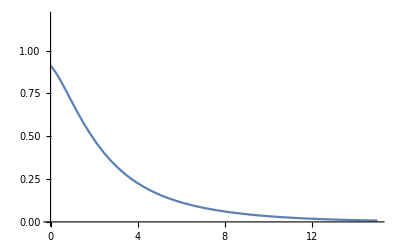

{{3.06122×10^-7,0.912874},{0.00460077,0.91225},{0.00920123,0.911619},{0.0184022,0.910336},{0.036804,0.907689},{0.0736077,0.90208},{0.147215,0.889729},{0.151816,0.888911},{0.156416,0.888089},{0.165617,0.886428},{0.184019,0.88305},{0.220823,0.876075},{0.29443,0.861342},{0.299417,0.86031},{0.304405,0.859274},{0.31438,0.85719},{0.334329,0.852977},{0.374229,0.844382},{0.454028,0.82661},{0.613625,0.78938},{0.911668,0.717274},{1.20386,0.647481},{1.52083,0.576068},{1.81664,0.514934},{2.13721,0.455265},{2.45194,0.403282},{2.74552,0.360336},{3.06386,0.319275},{3.36105,0.285573},{3.65239,0.256376},{3.9685,0.228475},{4.26346,0.205543},{4.58318,0.183621},{4.89706,0.16468},{5.18978,0.149014},{5.50727,0.133919},{5.80361,0.121384},{6.12471,0.109279},{6.43997,0.0986994},{6.73407,0.0898523},{7.05294,0.0812408},{7.35066,0.0740145},{7.64253,0.0676066},{7.95917,0.0613285},{8.25465,0.0560336},{8.5749,0.0508424},{8.8893,0.0462409},{9.18255,0.0423446},{9.50057,0.0385066},{9.79743,0.0352518},{10.0885,0.0323383},{10.4042,0.0294579},{10.6989,0.0270093},{11.0183,0.0245904},{11.3165,0.0225324},{11.6089,0.0206857},{11.9261,0.0188566},{12.2221,0.0172982},{12.5429,0.0157566},{12.8578,0.0143787},{13.1516,0.0132034},{13.4701,0.0120386},{13.7675,0.0110449},{14.059,0.010151},{14.3754,0.00926348},{14.6705,0.00850588},{14.6757,0.00849323},{14.6808,0.00848061},{14.6911,0.00845541},{14.7117,0.00840524},{14.7529,0.0083058},{14.8353,0.00811046},{14.8404,0.00809841},{14.8456,0.00808637},{14.8558,0.00806236},{14.8764,0.00801453},{14.9176,0.00791975},{14.9228,0.00790798},{14.9279,0.00789623},{14.9382,0.00787278},{14.9588,0.00782608},{14.964,0.00781446},{14.9691,0.00780284},{14.9794,0.00777967},{14.9846,0.00776811},{14.9897,0.00775657},{14.9949,0.00774505},{15.,0.00773354}}

C:\Users\Oscar\Documents\GitHub\MasterThesisCode\data\N2XOR_0T_GenErr.txt

```mathematica
Clear[Eg]
Eg[P_] = 2(1/4)^P (4RI[P]EgContrib[P, 1, 3/4, 1/2, 0, 1/4, 1/2] +  4RII[P]EgContrib[P, 1, 2/4, 1/4, 0, 0, 1/4] + 2RII[P]EgContrib[P, 1, 2/4, 0, 0, 0, 0] +  4RIII[P]EgContrib[P, 1, 1/4, 0, 0, 0, 0]  + RIV[P] EgContrib[P, 1,0, 0, 0, 0, 0]) ;

plot = Plot[Eg[P], {P, 0, 15}, PlotRange -> {0, 1.2}]
data = Cases[Cases[plot,Line[___],Infinity],{_?NumericQ,_?NumericQ},Infinity]
Export["C:\Users\Oscar\Documents\GitHub\MasterThesisCode\data\N2XOR_0T_GenErr.txt",data,"Table"]
```